```mathematica
$Version (*Mathematica version used to generate this file on April 14 2023.*)
```

12.0.0 for Microsoft Windows (64-bit) (April 6, 2019)

## 1. Distinct Mechanisms of PA

```mathematica
baseparams={KA->10,Kdim->0.1,RAF->0.04,f->0.01,g->100};(*units: μM ∀ params but KA*)
```

## Section 1.1. Dimer Potentiation (DP) Model

```mathematica
Quit[]
```

#### 1.1.1. Analytic Solution to the model

The assembled kinase state can dimerize (AA) or bind with  a drug (Ad). The kinase dimer (AA), upon drug administration can occur in either partly (AAd) or fully inhibited state (AdAd). The equilibrium state relationships and protein concentration conservation equations for both total RAF (RAF) and total drug (DTOT) are defined as follows.

```mathematica
vars={a,A,d,AA,Ad,AAd,AdAd};(*A list of all variables*)
rep1={AA->A^2/Kdim,AAd->(2 A^2 d)/(f Kdim Kd),AdAd->(A^2 d^2)/(f g Kdim Kd^2),Ad->(A d)/Kd,a->0}/.g->1; (*equations derived from equilibrium relationships*)
Consrv[eqns_]:={Simplify[eqns[[1]]+eqns[[2]]+eqns[[5]]+2(eqns[[4]]+eqns[[6]]+eqns[[7]])],Simplify[eqns[[3]]+eqns[[5]]+eqns[[6]]+2(eqns[[7]])]}(*conservation relations for RAF and DTOT*)
eqnsconsrv=Simplify[Thread[Simplify[Consrv[vars]/.rep1]=={RAF,DTOT}]] (*Solve the conservation equations simplifying to two variables RAF, DTOT using the equilibrium relationships above*)
```

{A (d+Kd+(2 A (d^2+2 d Kd+f Kd^2))/(f Kd Kdim))==Kd RAF,d+(A d)/Kd+(2 A^2 d (d+Kd))/(f Kd^2 Kdim)==DTOT}

A simultaneous solution to both the above conservation equations is unwieldy and hard to obtain. Instead, we find partial solutions for kinase protomers as a function of free drug and then free drug as a function of the total drug and the kinase protomers. The latter solution is used to construct d vs DTOT relationship and prove monotonocity thereof leading to a complete solution to PA existence problem.

```mathematica
SimplifyPars[x_]:=Simplify[x,{RAF>0,DTOT>0,Kd>0,Kdim>0,KA>0,d>0,f>0,g>0,Subscript[d, rel]>0}];
sol1A=SimplifyPars[Solve[eqnsconsrv[[1]],A]][[2]]  (*Second solution is positive*)
sol1d=SimplifyPars[Solve[eqnsconsrv[[2]],d]][[2]](*Second solution is positive*)
```

{A→(Kd (-d f Kdim-f Kd Kdim+√(f Kdim (f Kd^2 (Kdim+8 RAF)+d^2 (f Kdim+8 RAF)+2 d Kd (f Kdim+8 RAF)))))/(4 (d^2+2 d Kd+f Kd^2))}

{d→-(Kd (2 A^2+A f Kdim+f Kd Kdim-√(8 A^2 DTOT f Kdim+(2 A^2+A f Kdim+f Kd Kdim)^2)))/(4 A^2)}

We estimate the total activity by counting all of the drug-free protomers which occur within a partly active or fully active dimer. Substituting the above solution into the expression for Raf activity and dividing by total RAF concentration, we obtain the proportionate activity as a function of total drug and other parameters.

```mathematica
RafActivity[vars_]:= 2 vars[[4]] + vars[[6]]
fnActiveRAFDS=SimplifyPars[RafActivity[vars]/RAF/.rep1/.sol1A];
repratios={RAF->Kdim Subscript[RAF, rel],d->Kd Subscript[d, rel]};
fnActiveRAFDS=FullSimplify[fnActiveRAFDS/.repratios,{Kd>0,Kdim>0,RAF>0}]
fnActiveRAF2DS=FullSimplify[SimplifyPars[fnActiveRAFDS//.{Subscript[RAF, rel]->E2d/(8 f(f+2 Subscript[d, rel]+Subscript[d, rel]^2))}]/.Subscript[d, rel]->(E1d/f-1),{E1d>0,E2>0,f>0}]
```

((f+d_rel) (f+f d_rel-√(f (f (1+d_rel)^2+8 (f+d_rel (2+d_rel)) RAF_rel)))^2)/(8 f (f+d_rel (2+d_rel))^2 RAF_rel)

((E1d-√(E1d^2+E2d))^2 f (E1d+(-1+f) f))/(E2d (E1d^2+(-1+f) f^2))

Note that the above equations represent the total active RAF protomers in proportion to the total RAF kinase as a function of unbound drug (d). In order to analytically establish parameter values which correspond to activation of the kinase, we find the first derivative of the function fnActiveRAFDS and search for it’s zeroes in section 1.1.3.

First, we identify total RAF dimers and it’s proportion to active RAF dimers.

```mathematica
RafDimers[eqns_]:=(eqns[[4]]+eqns[[6]]+eqns[[7]]);
fnDimers=FullSimplify[SimplifyPars[(RafDimers[vars]/RAF/.rep1/.sol1A)/.repratios],Kd>0]
SimplifyPars[fnDimers/fnActiveRAFDS]
```

((f+f d_rel-√(f (f (1+d_rel)^2+8 (f+d_rel (2+d_rel)) RAF_rel)))^2)/(16 f (f+d_rel (2+d_rel)) RAF_rel)

(f+d_rel (2+d_rel))/(2 (f+d_rel))

#### 1.1.2. Baseline Signaling (drug-free)

```mathematica
baselineActiveRAFDS=SimplifyPars[fnActiveRAFDS/.Subscript[d, rel]->0]
FullSimplify[D[baselineActiveRAFDS,Subscript[RAF, rel]],Subscript[RAF, rel]>0]
```

(-1+√(1+8 RAF_rel))^2/(8 RAF_rel)

(-1+√(1+8 RAF_rel))^2/(8 RAF_rel^2 √(1+8 RAF_rel))

The derivative of baseline signaling relative to RAF_rel is a positive definite function. Therefore, baseline signaling is a monotonically proportionate to RAF_rel, which is in turn, monotonically proportionate to RAF concentration and monotonically inverse relationship to Kdim.

Hence in the DS model, increasing RAF_rel  increases baseline signaling. This is a simple analytic cross-check of expected behaviors in this model.

#### 1.1.3. Conditions on parameter regions for activation in response to the drug

```mathematica
dfn12=SimplifyPars[D[fnActiveRAFDS,Subscript[d, rel]]]
```

1/(8 f (f+d_rel (2+d_rel))^3 RAF_rel)(f+f d_rel-√(f (f (1+d_rel)^2+8 (f+d_rel (2+d_rel)) RAF_rel))) (2 (f+d_rel) (f+d_rel (2+d_rel)) (f-(f (1+d_rel) (f+8 RAF_rel))/(√(f (f (1+d_rel)^2+8 (f+d_rel (2+d_rel)) RAF_rel))))-4 (1+d_rel) (f+d_rel) (f+f d_rel-√(f (f (1+d_rel)^2+8 (f+d_rel (2+d_rel)) RAF_rel)))+(f+d_rel (2+d_rel)) (f+f d_rel-√(f (f (1+d_rel)^2+8 (f+d_rel (2+d_rel)) RAF_rel))))

```mathematica
existPADS=SimplifyPars[Reduce[dfn12>0]]
```

(0<RAF_rel<(f (f (3-8 f+4 f^2)+(2-6 f) d_rel-(1+f+4 f^2) d_rel^2-4 f d_rel^3-d_rel^4))/(8 (f+2 f d_rel+d_rel^2)^2)&&2 f+d_rel<1&&d_rel≤1)||(-(f (1+d_rel)^2)/(8 (f+2 d_rel+d_rel^2))<RAF_rel<0&&f>1)||((f (f (3-8 f+4 f^2)+(2-6 f) d_rel-(1+f+4 f^2) d_rel^2-4 f d_rel^3-d_rel^4))/(8 (f+2 f d_rel+d_rel^2)^2)<RAF_rel<0&&f≤1&&(d_rel>1||2 f+d_rel>1))

Conditions for positive derivative of active RAF relative to unbound drug are shown above. However, RAF concentration is a positive definite quantity.

```mathematica
existPADS=Simplify[existPADS,Subscript[RAF, rel]>0]
```

RAF_rel<(f (f (3-8 f+4 f^2)+(2-6 f) d_rel-(1+f+4 f^2) d_rel^2-4 f d_rel^3-d_rel^4))/(8 (f+2 f d_rel+d_rel^2)^2)&&2 f+d_rel<1&&d_rel≤1

The above condition is realizable only when, the second and third conditions are true:  d<Kd(1-2f) and d<Kd. The latter condition is automatically true  when former one is. Further, the former condition can only be true when 2f<1, i.e. f<0.5 instead of f<1: which one would naively expect.

The first condition can only be True when the RHS is positive, since LHS is always so.

```mathematica
existPADS2=SimplifyPars[Reduce[(existPADS[[1]][[2]]>0)]]
```

(2 f+d_rel<1&&d_rel≤1)||f>1/4 (3+d_rel+2 d_rel^2+(1+d_rel) √(9+4 d_rel+4 d_rel^2))

The first condition is identical to second and third conditions of existPADS which implies that f<0.5. The second alternate condition is f>3/4 + a positive number, which is a direct contradiction. Only one of these conditions can be satisfied. However, since the logic of existPADS equation is (A|B)&A the solution is A alone.

```mathematica
existPADS[[2]]
```

2 f+d_rel<1

Hence we derive the above, necessary but not sufficient condition for PA. It also suggests that for sufficiently small concentration of RAF and sufficiently small f, there is a small enough concentration of drug for which PA will be observed within this model. 
Also, since d_rel<DTOT/Kd, 2f<1-d_rel is automatically satisfied if 2f<1-DTOT/Kd.
A corollary: with sufficiently high drug concentration, this condition cannot be satisfied. That is a validation that this model does not support motonic rise in activation in repsonse to the drug, eventually, the activity gets reduced.

Can PA exist even when above conditions are not satisfied? That is the first derivative of active RAF relative to drug is negative near zero drug but then becomes positive? And then negative again (since high drug conc have to go to zero)? - the possibility cannot be ruled out at this stage. This is why the conditions are necessary but not sufficient.

#### 1.1.4. Monotonic relationship between unbound (d) and total (DTOT) drug concentrations

For some of the conclusions with regards to PA to hold, the relationship between unbount and total drug has to be monotonic.

```mathematica
eqnsconsrv[[2]]
```

d+(A d)/Kd+(2 A^2 d (d+Kd))/(f Kd^2 Kdim)==DTOT

The derivative of the function DTOT relative to d is the sum of the derivative of different terms within the second equation in expression above. Among these the derivative of the first term is 1. And the derivative of the second and third term are shown as non-negative functions of unbound drug d, below.

```mathematica
sd11=FullSimplify[SimplifyPars[D[A*d/.sol1A,d]]];
rd11=Reduce[sd11<0];
SimplifyPars[rd11]
```

False

The first component is positive definite.

```mathematica
sd12=SimplifyPars[D[Simplify[A^2 d (d+Kd)/.sol1A],d]]
```

1/(16 (d^2+2 d Kd+f Kd^2)^3)Kd^2 (d f Kdim+f Kd Kdim-√(f Kdim (f Kd^2 (Kdim+8 RAF)+d^2 (f Kdim+8 RAF)+2 d Kd (f Kdim+8 RAF)))) (2 d (d+Kd) (d^2+2 d Kd+f Kd^2) (f Kdim-(f (d+Kd) Kdim (f Kdim+8 RAF))/(√(f Kdim (f Kd^2 (Kdim+8 RAF)+d^2 (f Kdim+8 RAF)+2 d Kd (f Kdim+8 RAF)))))-4 d (d+Kd)^2 (d f Kdim+f Kd Kdim-√(f Kdim (f Kd^2 (Kdim+8 RAF)+d^2 (f Kdim+8 RAF)+2 d Kd (f Kdim+8 RAF))))+d (d^2+2 d Kd+f Kd^2) (d f Kdim+f Kd Kdim-√(f Kdim (f Kd^2 (Kdim+8 RAF)+d^2 (f Kdim+8 RAF)+2 d Kd (f Kdim+8 RAF))))+(d+Kd) (d^2+2 d Kd+f Kd^2) (d f Kdim+f Kd Kdim-√(f Kdim (f Kd^2 (Kdim+8 RAF)+d^2 (f Kdim+8 RAF)+2 d Kd (f Kdim+8 RAF)))))

Note that the first non-trivial product term in this expression is negative definite. This is because the term inside the square root is always greater than the term outside. So we focus on the second, larger term.

```mathematica
sd121=FullSimplify[sd12[[-1]]];
rd12=Reduce[sd121>0];
SimplifyPars[rd12]
```

False

Since the expression sd121 is never positive. Also, the coefficient to sd121 in sd12 is negative definite as stated above. Therefore the full expression sd12 which a product of the two is non negative for all positive values of the parameters.

DTOT=d+sd11+sd12

Since all three expressions on RHS are non-negative derivatives as a function of unbound drug - the total drug has a non-negative derivative. Therefore, DTOT(d) is monotonically positive/increasing function.
We exemplify this point numerically with an example set of parameters in the plot below.

```mathematica
fnDTOT=SimplifyPars[eqnsconsrv[[2]][[1]]/.rep1/.sol1A]
```

d+(d (d+Kd) (d f Kdim+f Kd Kdim-√(f Kdim (f Kd^2 (Kdim+8 RAF)+d^2 (f Kdim+8 RAF)+2 d Kd (f Kdim+8 RAF))))^2)/(8 f (d^2+2 d Kd+f Kd^2)^2 Kdim)+(d (-d f Kdim-f Kd Kdim+√(f Kdim (f Kd^2 (Kdim+8 RAF)+d^2 (f Kdim+8 RAF)+2 d Kd (f Kdim+8 RAF)))))/(4 (d^2+2 d Kd+f Kd^2))

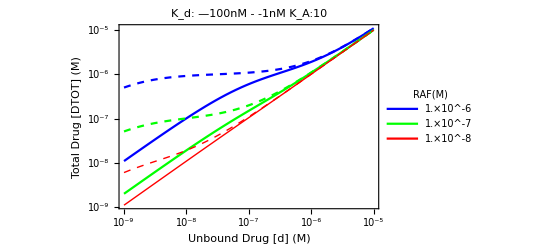

```mathematica
Sty[x_]:=Style[x,20,FontFamily->"Arial"];
KTarr={1. 10^-6,1. 10^-7,1. 10^-8};
kdarr={Kd-> 1. 10^-7 ,Kd-> 1. 10^-9};
pltfn=Flatten[Table[fnDTOT/.kd,{kd,kdarr},{RAF,KTarr}]]/.baseparams;
ps={Blue,Green,Directive[Red,Thick],Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Red,Dashed,Thick]};
LogLogPlot[pltfn,{d,10^-9,10^-5},Frame->True,FrameTicksStyle->20,PlotStyle->ps,PlotLegends->Placed[LineLegend[ {Blue,Green,Directive[Red,Thick]},Sty/@KTarr,LegendLabel->Sty["RAF(M)"],LegendFunction->Panel,LabelStyle->12],{Right,Bottom}],FrameLabel->(Sty/@{"Unbound Drug [d] (M)","Total Drug [DTOT] (M)"}),ImageSize->{500},FrameStyle->Thickness[0.004],PlotLabel->Sty["K_d: —100nM  - -1nM K_A:10"](*N[TableForm[parset01,TableDirections->Row]]*)]
```

#### 1.1.5. Analytic Expressions for maximum Fold Change (FC)

Fold change is defined as the ratio between maximum RAF activity (active protomers) to that in absence of drug

```mathematica
rafFC=SimplifyPars[fnActiveRAFDS/baselineActiveRAFDS]
```

((f+d_rel) (f+f d_rel-√(f (f (1+d_rel)^2+8 (f+d_rel (2+d_rel)) RAF_rel)))^2)/(f (f+d_rel (2+d_rel))^2 (-1+√(1+8 RAF_rel))^2)

Activating Range is defined as the lowest concentration above which the drug no longer acts as a paradoxical activator and becomes an inhibitor. This function is not easily solved analytically, and to understand its variation within the range of parameters defined in conditions for PA above, is calculated numerically.

## Section 1.2. Negative Cooperativity (NC) Model

```mathematica
Quit[]
```

#### 1.2.1. Analytic Solution to the model

The assembled kinase state can dimerize (AA) or bind with  a drug (Ad). The kinase dimer (AA), upon drug administration can occur in either partly (AAd) or fully inhibited state (AdAd). The equilibrium state relationships and protein concentration conservation equations for both total RAF (RAF) and total drug (DTOT) are defined as follows.

```mathematica
vars={a,A,d,AA,Ad,AAd,AdAd};(*A list of all variables*)
rep2={AA->A^2/Kdim,AAd->(2 A^2 d)/(f Kdim Kd),AdAd->(A^2 d^2)/(f g Kdim Kd^2),Ad->(A d)/Kd,a->0}/.f->1; (*derived from equilibrium relationships*)
Consrv[eqns_]:={Simplify[eqns[[1]]+eqns[[2]]+eqns[[5]]+2(eqns[[4]]+eqns[[6]]+eqns[[7]])],Simplify[eqns[[3]]+eqns[[5]]+eqns[[6]]+2(eqns[[7]])]};(*conservation relations for RAF and DTOT*)
eqnsconsrv=Simplify[Thread[Simplify[Consrv[vars]/.rep2]=={RAF,DTOT}]]
```

{A (d+Kd+(2 A (d^2+2 d g Kd+g Kd^2))/(g Kd Kdim))==Kd RAF,d+(A d)/Kd+(2 A^2 d (d+g Kd))/(g Kd^2 Kdim)==DTOT}

A simultaneous solution to both the above conservation equations is unwieldy and hard to obtain. Instead, we find partial solutions for kinase protomers as a function of free drug and then free drug as a function of the total drug and the kinase protomers. The latter solution is used to numerically construct d vs DTOT relationship.

```mathematica
SimplifyPars[x_]:=Simplify[x,{RAF>0,DTOT>0,Kd>0,Kdim>0,KA>0,d>0,f>0,g>0,Subscript[d, rel]>0,Subscript[RAF, rel]>0}];
sol2A=SimplifyPars[Solve[eqnsconsrv[[1]],A]][[2]]  (*Second solution is positive*)
sol2d=SimplifyPars[Solve[eqnsconsrv[[2]],d]][[2]](*Second solution is positive*)
```

{A→-(g Kd Kdim (d+Kd-√((2 d g Kd (Kdim+8 RAF)+g Kd^2 (Kdim+8 RAF)+d^2 (g Kdim+8 RAF))/(g Kdim))))/(4 (d^2+2 d g Kd+g Kd^2))}

{d→-(g Kd (2 A^2+A Kdim+Kd Kdim+√((8 A^2 DTOT Kdim+g (2 A^2+A Kdim+Kd Kdim)^2)/g)))/(4 A^2)}

We estimate the total activity by counting all of the drug-free protomers which occur within a partly active or fully active dimer. Substituting the above solution into the expression for Raf activity and dividing by total RAF concentration, we obtain the proportionate activity as a function of total drug and other parameters.

```mathematica
RafActivity[vars_]:= 2 vars[[4]] + vars[[6]]
fnActiveRAF=SimplifyPars[RafActivity[vars]/RAF/.rep2/.sol2A];
repratios={Kdim->RAF/Subscript[RAF, rel],d->Kd Subscript[d, rel]};
fnActiveRAFNC=SimplifyPars[FullSimplify[fnActiveRAF/.repratios]]
fnActiveRAF2NC=FullSimplify[SimplifyPars[fnActiveRAFNC//.{(1+Subscript[d, rel])->E1n,Subscript[RAF, rel]->E2n/(g+2g Subscript[d, rel]+Subscript[d, rel]^2)/8}]]
```

(g^2 (1+d_rel) (1+d_rel-√((1+d_rel)^2+(8 (g+2 g d_rel+d_rel^2) RAF_rel)/g))^2)/(8 (g+2 g d_rel+d_rel^2)^2 RAF_rel)

(E1n (E1n-√(E1n^2+E2n/g))^2 g^2)/(E2n (g+2 g d_rel+d_rel^2))

Note that the above equations represent the total active RAF protomers in proportion to the total RAF kinase as a function of unbound drug (d). In order to analytically establish parameter values which correspond to activation of the kinase, we find the first derivative of this function and search for it’s zeroes.

```mathematica
RafDimers[eqns_]:=(eqns[[4]]+eqns[[6]]+eqns[[7]]);
fnDimersNC=FullSimplify[SimplifyPars[(RafDimers[vars]/RAF/.rep2/.sol2A)/.repratios]]
SimplifyPars[fnDimersNC/fnActiveRAFNC]
```

(g (1+d_rel-√((1+d_rel)^2+(8 (g+2 g d_rel+d_rel^2) RAF_rel)/g))^2)/(16 (g+2 g d_rel+d_rel^2) RAF_rel)

(g+2 g d_rel+d_rel^2)/(2 g+2 g d_rel)

#### 1.2.2. Baseline Signaling (drug-free)

```mathematica
baselineActiveRAFNC=fnActiveRAFNC/.Subscript[d, rel]->0
SimplifyPars[D[baselineActiveRAFNC,Subscript[RAF, rel]]]
```

(1-√(1+8 RAF_rel))^2/(8 RAF_rel)

(-1+√(1+8 RAF_rel))^2/(8 RAF_rel^2 √(1+8 RAF_rel))

The derivative of baseline signaling relative to RAF_rel is a positive definite function. Therefore, baseline signaling is a monotonically proportionate to RAF_rel.

#### 1.2.3. Conditions on parameter regions for activation in response to the drug

```mathematica
dfn2=SimplifyPars[D[fnActiveRAFNC,Subscript[d, rel]]]
```

1/(8 (g+2 g d_rel+d_rel^2)^3 RAF_rel)g^2 (1+d_rel-√((1+d_rel)^2+(8 (g+2 g d_rel+d_rel^2) RAF_rel)/g)) (-4 (1+d_rel) (g+d_rel) (1+d_rel-√((1+d_rel)^2+(8 (g+2 g d_rel+d_rel^2) RAF_rel)/g))+(g+2 g d_rel+d_rel^2) (1+d_rel-√((1+d_rel)^2+(8 (g+2 g d_rel+d_rel^2) RAF_rel)/g))+2 (1+d_rel) (g+2 g d_rel+d_rel^2) (1+(-g (1+8 RAF_rel)-d_rel (g+8 RAF_rel))/(g √((1+d_rel)^2+(8 (g+2 g d_rel+d_rel^2) RAF_rel)/g))))

```mathematica
existPANC=SimplifyPars[Reduce[(dfn2>0)]]
```

False

Therefore, the derivative of active RAF relative to unbound drug may never be positive, independent of the drug concentration and negative cooperativity. This mechanism does not produce PA.

#### 1.2.5. Analytic Expressions for maximum Fold Change (FC)

Fold change is defined as the ratio between maximum RAF activity (no/conc of active protomers) to that in absence of drug

```mathematica
maxActiveRAFNC=FullSimplify[SimplifyPars[fnActiveRAFNC]];
rafFC=SimplifyPars[maxActiveRAFNC/baselineActiveRAFNC]
```

(g^2 (1+d_rel) (1+d_rel-√((1+d_rel)^2+(8 (g+2 g d_rel+d_rel^2) RAF_rel)/g))^2)/((g+2 g d_rel+d_rel^2)^2 (-1+√(1+8 RAF_rel))^2)

```mathematica
dRAFrafFC=SimplifyPars[D[rafFC,Subscript[RAF, rel]]];
dgrafFC=SimplifyPars[D[rafFC,g]];
SimplifyPars[Reduce[dRAFrafFC>0]]
SimplifyPars[Reduce[dgrafFC>0]]
```

g>1

True

Hence, first derivative of the fold change expression relative to RAF_rel is always positive in the negative cooperativity model and always negative in positive cooperativity model. That is when g>1: negative cooperativity mediates increase in activity with increase in [RAF].

Even though fold change is not paradoxical (PA<1), as negative cooperativity increases, fold change increases. In other mechanisms where PA exists, negative cooperativity increases PA further.

## Section 1.3. Conformal Autoinhibition (CA/base) Model

```mathematica
Quit[]
```

#### 1.3.1. Analytic Solution to the model

This model incorporates all the mechanisms from the part models to combine into a model of kinase which auto-inhibits (a), which, for simplicity, is modeled to relieve at a first order rate to an assembled state (A). The assembled kinase state can dimerize (AA) or bind with  a drug (Ad). The kinase dimer (AA), upon drug administration can occur in either partly (AAd) or fully inhibited state (AdAd). The equilibrium state relationships and protein concentration conservation equations for both total RAF (RAF) and total drug (DTOT) are defined as follows.

```mathematica
vars={a,A,d,AA,Ad,AAd,AdAd};(*A list of all variables*)
rep3={AA->A^2/Kdim,AAd->(2 A^2 d)/(f Kdim Kd),AdAd->(A^2 d^2)/(f g Kdim Kd^2),Ad->(A d)/Kd,a->A KA}/.{f->1,g->1}; (*derived from equilibrium relationships*)
Consrv[eqns_]:={Simplify[eqns[[1]]+eqns[[2]]+eqns[[5]]+2(eqns[[4]]+eqns[[6]]+eqns[[7]])],Simplify[eqns[[3]]+eqns[[5]]+eqns[[6]]+2(eqns[[7]])]};(*conservation relations for RAF and DTOT*)
eqnsconsrv=Simplify[Thread[Simplify[Consrv[vars]/.rep3]=={RAF,DTOT}]]
```

{(A (2 A (d+Kd)^2+Kd (d+Kd+KA Kd) Kdim))/(Kd^2 Kdim)==RAF,d+(A d)/Kd+(2 A^2 d (d+Kd))/(Kd^2 Kdim)==DTOT}

A simultaneous solution to both the above conservation equations is unwieldy and hard to obtain. Instead, we find partial solutions for kinase protomers as a function of free drug and then free drug as a function of the total drug and the kinase protomers. The latter solution is used to numerically construct d vs DTOT relationship.

```mathematica
SimplifyPars[x_]:=Simplify[x,{RAF>0,DTOT>0,Kd>0,Kdim>0,KA>0,d>0,f>0,g>0}];
sol3A=SimplifyPars[Solve[eqnsconsrv[[1]],A]][[2]]  (*Second solution is positive*)
sol3d=SimplifyPars[Solve[eqnsconsrv[[2]],d]][[2]](*Second solution is positive*)
```

{A→-1/(4 (d+Kd)^2)Kd Kdim (d+Kd+KA Kd-√(((d+Kd+KA Kd)^2 Kdim+8 (d+Kd)^2 RAF)/Kdim))}

{d→-(Kd (2 A^2+A Kdim+Kd Kdim-√(8 A^2 DTOT Kdim+(2 A^2+A Kdim+Kd Kdim)^2)))/(4 A^2)}

We estimate the total activity by counting all of the drug-free protomers which occur within a partly active or fully active dimer. Substituting the above solution into the expression for Raf activity and dividing by total RAF concentration, we obtain the proportionate activity as a function of total drug and other parameters.

```mathematica
RafActivity[vars_]:= 2 vars[[4]] + vars[[6]]
fnActiveRAF=SimplifyPars[RafActivity[vars]/RAF/.rep3/.sol3A];
repratios={Kdim->RAF/Subscript[RAF, rel],d->Kd Subscript[d, rel]};
fnActiveRAFCA=SimplifyPars[FullSimplify[fnActiveRAF/.repratios]]
fnActiveRAF2CA=FullSimplify[SimplifyPars[fnActiveRAFCA//.{(1+KA+Subscript[d, rel])->E1c,Subscript[RAF, rel]->E2c /(1+2 Subscript[d, rel]+Subscript[d, rel]^2)/8}]]
```

((1+KA+d_rel-√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel))^2)/(8 (1+d_rel)^3 RAF_rel)

((E1c-√(E1c^2+E2c))^2)/(E2c (1+d_rel))

##### Test the hypothesis that the auto-inhibition model and dimer potentiation model can be inter-converted upon parametric transformation

```mathematica
SimplifyPars[Solve[(Kd (-d f Kdim-f Kd Kdim+√(f Kdim (f Kd^2 (Kdim+8 RAF)+d^2 (f Kdim+8 RAF)+2 d Kd (f Kdim+8 RAF)))))/(4 (d^2+2 d Kd+f Kd^2))==(Kd Kdim (d+Kd+KA Kd-√(((d+Kd+KA Kd)^2 Kdim+8 (d+Kd)^2 RAF)/Kdim)))/(4 (d+Kd)^2),f]]
```

{{f→-((d (d+2 Kd) (2 d^2 (Kdim+2 RAF)+d Kd ((4+3 KA) Kdim+8 RAF)-2 d √(Kdim (d^2 (Kdim+8 RAF)+2 d Kd (Kdim+KA Kdim+8 RAF)+Kd^2 ((1+KA)^2 Kdim+8 RAF)))+(2+KA) Kd ((1+KA) Kd Kdim-√(Kdim (d^2 (Kdim+8 RAF)+2 d Kd (Kdim+KA Kdim+8 RAF)+Kd^2 ((1+KA)^2 Kdim+8 RAF))))))/(2 (6 d (2+KA) Kd^3 Kdim+(2+KA)^2 Kd^4 Kdim+d^3 Kd ((8+KA) Kdim-8 RAF)+d^2 Kd^2 ((14+3 KA) Kdim-8 RAF)+2 d^4 (Kdim-RAF))))}}

Note that the above equations represent the total active RAF protomers in proportion to the total RAF kinase as a function of unbound drug (d). In order to analytically establish parameter values which correspond to activation of the kinase, we find the first derivative of this function (equation 11) and search for it’s zeroes (equation 12).

```mathematica
RafDimers[eqns_]:=(eqns[[4]]+eqns[[6]]+eqns[[7]]);
fnDimersCA=FullSimplify[SimplifyPars[(RafDimers[vars]/RAF/.rep3/.sol3A)/.repratios]]
SimplifyPars[fnDimersCA/fnActiveRAFCA]
```

((1+KA+d_rel-√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel))^2)/(16 (1+d_rel)^2 RAF_rel)

1/2 (1+d_rel)

#### 1.3.2. Baseline Signaling (drug-free)

```mathematica
baselineActiveRAFCA=fnActiveRAFCA/.Subscript[d, rel]->0;
rep3b={Subscript[RAF, rel]->E3(1+KA)^2/8};
baselineActiveRAF1=SimplifyPars[baselineActiveRAFCA/.rep3b]
SimplifyPars[D[baselineActiveRAF1,E3]/.rep3b]
```

(-1+√(1+E3))^2/E3

(-1+√(1+E3))^2/(E3^2 √(1+E3))

The derivative of baseline signaling relative to E3 is a positive definite function. Therefore, baseline signaling is a monotonically proportionate to E3, which is in turn, monotonically proportionate to RAF concentration and monotonically inverse relationship to KA.

Hence in the base model, increasing KA decreases baseline signaling and increasing RAF_rel  increases baseline signaling.

#### 1.3.3. Conditions on parameter regions for activation in response to the drug

```mathematica
dfn3=SimplifyPars[D[fnActiveRAFCA,Subscript[d, rel]]]
```

1/(8 (1+d_rel)^4 RAF_rel)(1+KA+d_rel-√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)) (2 (1+d_rel) (1-(1+KA+d_rel+8 (1+d_rel) RAF_rel)/(√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)))-3 (1+KA+d_rel-√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)))

```mathematica
Simplify[SimplifyPars[dfn3//.{(1+KA+Subscript[d, rel])->E1,Subscript[RAF, rel]->E2 /(1+2 Subscript[d, rel]+Subscript[d, rel]^2)/8}],{E1>0,E2>0,Subscript[d, rel]>0}]
```

-((-E1+√(E1^2+E2)) (3 E1^2+E2+2 √(E1^2+E2)-E1 (2+3 √(E1^2+E2))+2 (-E1+√(E1^2+E2)) d_rel))/(E2 √(E1^2+E2) (1+d_rel)^2)

The first two roots are complex coming from the first bracket term.

```mathematica
zeroes=SimplifyPars[Solve[dfn3==0,Subscript[d, rel],VerifySolutions->True]]
```

{{d_rel→-(1+KA+8 RAF_rel+2 KA √(1+6 RAF_rel))/(1+8 RAF_rel)},{d_rel→-(1+KA+8 RAF_rel-2 KA √(1+6 RAF_rel))/(1+8 RAF_rel)}}

The first solution is negative definite. Below, we derive the rules (expression 13) which allow the second solution to be positive

```mathematica
exist=Reduce[((Subscript[d, rel]/.zeroes[[2]])>0)&&(KA>0)&&(Subscript[RAF, rel]>0)]
```

KA>1&&0<RAF_rel<1/8 (-1-2 KA+3 KA^2)

Hence with a sufficiently small ratio of raf concentration to dimerization constant ratio, the auto-inhibition mechanism can by itself mediate activation of the kinase in response to drug administration.

In section 1.2 we will show that our analytic results as a function of unbound drug concentration also extend to the complete case where we consider the relationship between unbound and bound drug.

To establish that the above constraints imply existence of activation (maxima), we derive the second derivative of fnActiveRAFCA, find it’s value at the critical point in variable ‘zeroes’. We then find the conditions under which this function is negative.

```mathematica
d2fn3=SimplifyPars[D[dfn3,Subscript[d, rel]]]
```

1/(8 (1+d_rel)^5 RAF_rel)((1+d_rel) (1+KA+d_rel-√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)) (-1-(16 KA^2 (1+d_rel) RAF_rel)/(((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)^(3/2))-(2 (1+KA+d_rel+8 (1+d_rel) RAF_rel))/(√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel))+(3 (1+KA+8 RAF_rel+d_rel (1+8 RAF_rel)))/(√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)))+(1+d_rel) (1-(1+KA+d_rel+8 (1+d_rel) RAF_rel)/(√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel))) (2 (1+d_rel) (1-(1+KA+d_rel+8 (1+d_rel) RAF_rel)/(√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)))-3 (1+KA+d_rel-√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)))-4 (1+KA+d_rel-√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)) (2 (1+d_rel) (1-(1+KA+d_rel+8 (1+d_rel) RAF_rel)/(√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel)))-3 (1+KA+d_rel-√((1+KA+d_rel)^2+8 (1+d_rel)^2 RAF_rel))))

```mathematica
d2fn3z=FullSimplify[d2fn3/.zeroes[[2]],{KA>0,Subscript[RAF, rel]>0}]
```

1/(162 KA^3 RAF_rel)(1-√(1+6 RAF_rel)+3 RAF_rel (6-5 √(1+6 RAF_rel)-24 RAF_rel (-1+√(1+6 RAF_rel))))

```mathematica
FullSimplify[Numerator[d2fn3z]/.{Subscript[RAF, rel]->(a^2-1)/6},a>0]/.a->√(1+6 Subscript[RAF, rel])
```

-1/2 √(1+6 RAF_rel) (1+√(1+6 RAF_rel)-2 (1+6 RAF_rel))^2

```mathematica
Reduce[(d2fn3z<0)&&(KA>=0)&&(Subscript[RAF, rel]>=0)]
```

KA>0&&RAF_rel>0

No additional constraints from second derivative condition that the critical point be a maxima. The ‘exist’ condition above is necessary and sufficient as long as monotonocity between unbound and total drug can be established.

#### 1.3.4. Monotonic relationship between unbound (d) and total (DTOT) drug concentrations

The derivative of the function DTOT relative to unbound drug d is the sum of the derivative of different composing terms. Among these the derivative of the first term is 1. And the derivative of the second and third term are shown as non-negative functions of unbound drug d, below.

```mathematica
sd311=FullSimplify[SimplifyPars[D[A*d/.sol3A,d]]];
rd311=Reduce[sd311<0];
SimplifyPars[rd311]
```

(3 d≤Kd||d<Kd)&&(d<Kd<3 d||KA<(d+Kd)/(d-Kd)||Kd>3 d)&&((d+Kd)/(d-Kd)<KA<Kd/(d-Kd)||KA<(d+Kd)/(d-Kd))&&d (Kdim-KA^2 Kdim+8 RAF)+Kd ((1+KA)^2 Kdim+8 RAF)<0

```mathematica
sd312=SimplifyPars[D[Simplify[A^2 d (d+Kd)/.sol3A],d]]
```

1/(16 (d+Kd)^4)Kd^2 Kdim^2 (d+Kd+KA Kd-√(((d+Kd+KA Kd)^2 Kdim+8 (d+Kd)^2 RAF)/Kdim)) (-3 d (d+Kd+KA Kd-√(((d+Kd+KA Kd)^2 Kdim+8 (d+Kd)^2 RAF)/Kdim))+(d+Kd) (d+Kd+KA Kd-√(((d+Kd+KA Kd)^2 Kdim+8 (d+Kd)^2 RAF)/Kdim))+2 d (d+Kd) (1+(-d (Kdim+8 RAF)-Kd (Kdim+KA Kdim+8 RAF))/(√(Kdim ((d+Kd+KA Kd)^2 Kdim+8 (d+Kd)^2 RAF)))))

Note that the first non-trivial product term in this expression is negative definite as the term inside the square root is always greater than the term outside. So we focus on the second term.

```mathematica
sd3121=FullSimplify[sd312[[-1]]];
rd312=Reduce[sd3121>0];
SimplifyPars[SimplifyPars[rd312]]
```

Kd>2 d&&((d+Kd)/(2 d-Kd)<KA<-(Kd (d+Kd))/(-4 d^2+Kd^2)||KA<(d+Kd)/(2 d-Kd))&&((d^2 (1-4 KA^2)+2 d (1+KA) Kd+(1+KA)^2 Kd^2) Kdim)/(8 (d+Kd)^2)+RAF<0

The first two conditions imply:  d<Kd/2 combined with KA<~1/(2d-Kd) which gives KA<0. As KA is positive definite, the expression sd3121 is non positive. Also, the coefficient to sd3121 in sd312 is negative definite as stated above. Therefore the full expression sd12 is non negative for all positive values of the parameters.

DTOT=d+sd11+sd12

Since all three expressions on RHS are non-negative derivatives as a function of unbound drug - the total drug has a non-negative derivative. Therefore, DTOT(d) is monotonically positive/increasing function.
We show this point with an example set of parameters in the plot below.

```mathematica
fnDTOT=SimplifyPars[Consrv[vars][[2]]/.rep3/.sol3A];
```

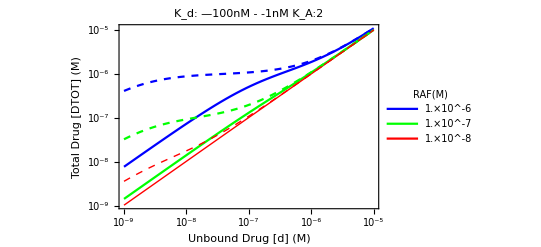

```mathematica
Sty[x_]:=Style[x,20,FontFamily->"Arial"];
parset01={KA->2.,Kdim-> 1. 10^-7 (*100nM*),f->0.01,g->4};
KTarr={1. 10^-6,1. 10^-7,1. 10^-8};
kdarr={Kd-> 1. 10^-7 ,Kd-> 1. 10^-9};
pltfn=Flatten[Table[fnDTOT/.parset01/.kd,{kd,kdarr},{RAF,KTarr}]];
ps={Blue,Green,Directive[Red,Thick],Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Red,Dashed,Thick]};
LogLogPlot[pltfn,{d,10^-9,10^-5},Frame->True,FrameTicksStyle->20,PlotStyle->ps,PlotLegends->Placed[LineLegend[ {Blue,Green,Directive[Red,Thick]},Sty/@KTarr,LegendLabel->Sty["RAF(M)"],LegendFunction->Panel,LabelStyle->12],{Right,Bottom}],FrameLabel->(Sty/@{"Unbound Drug [d] (M)","Total Drug [DTOT] (M)"}),ImageSize->{500},FrameStyle->Thickness[0.004],PlotLabel->Sty["K_d: —100nM  - -1nM K_A:2"](*N[TableForm[parset01,TableDirections->Row]]*)]
```

#### 1.3.5. Analytic Expressions for maximum Fold Change (FC)

Fold change is defined as the ratio between maximum RAF activity (no/conc of active protomers) to that in absence of drug

```mathematica
maxActiveRAFCA=FullSimplify[SimplifyPars[fnActiveRAFCA/.zeroes[[2]]]];
rafFC=SimplifyPars[maxActiveRAFCA/baselineActiveRAFCA]
```

(8 (-1+√(1+6 RAF_rel)+RAF_rel (-9+6 √(1+6 RAF_rel))))/(27 KA (1+KA-√((1+KA)^2+8 RAF_rel))^2)

When the ‘exist’ conditions derived above to qualify for existence of PA within this model are satisfied, we can evaluate the functional dependence of the raf fold change expression on RAF_rel and KA:

```mathematica
dRAFrafFC=SimplifyPars[D[rafFC,Subscript[RAF, rel]]]
dKArafFC=SimplifyPars[D[rafFC,KA]]
Simplify[Reduce[dRAFrafFC<0],exist]
Simplify[Reduce[dKArafFC>0],exist]
```

(8 ((9 (-1-6 RAF_rel+√(1+6 RAF_rel)) (-1-KA+√((1+KA)^2+8 RAF_rel)))/(√(1+6 RAF_rel))+(8 (-1+√(1+6 RAF_rel)+RAF_rel (-9+6 √(1+6 RAF_rel))))/(√((1+KA)^2+8 RAF_rel))))/(27 KA (1+KA-√((1+KA)^2+8 RAF_rel))^3)

-(8 (-2 KA+√((1+KA)^2+8 RAF_rel)) (-1+√(1+6 RAF_rel)+RAF_rel (-9+6 √(1+6 RAF_rel))))/(27 KA^2 √((1+KA)^2+8 RAF_rel) (1+KA-√((1+KA)^2+8 RAF_rel))^2)

True

True

Hence, first derivative of the fold change expression relative to KA is always positive when the model displays PA and the first derivative relative to RAF rel always negative. 
In other words, an equilibrium that more and more favors the inactive state (increasing KA), the fold change continues to increase as a function of KA. And as the concentration of RAF increases or it’s dimerization rate increases (Kdim reduces), the fold change relative to baseline continues to reduce.

```mathematica
{maxActiveRAFCA,baselineActiveRAFCA}
```

{(-1+√(1+6 RAF_rel)+RAF_rel (-9+6 √(1+6 RAF_rel)))/(27 KA RAF_rel),((1+KA-√((1+KA)^2+8 RAF_rel))^2)/(8 RAF_rel)}

Activating Range is defined as the lowest concentration above which the drug no longer acts as a paradoxical activator and becomes an inhibitor. This function is not easily solved analytically, and to understand its variation within the range of parameters defined in conditions for PA above, is calculated numerically in python files.

## Section 1.4. Unified Model

```mathematica
Quit[]
```

#### 1.4.1. Analytic Solution to the model

This model incorporates all the mechanisms.

```mathematica
vars={a,A,d,AA,Ad,AAd,AdAd};(*A list of all variables*)
rep4={AA->A^2/Kdim,AAd->(2 A^2 d)/(f Kdim Kd),AdAd->(A^2 d^2)/(f g Kdim Kd^2),Ad->(A d)/Kd,a->A KA}; (*derived from equilibrium relationships*)
Consrv[eqns_]:={Simplify[eqns[[1]]+eqns[[2]]+eqns[[5]]+2(eqns[[4]]+eqns[[6]]+eqns[[7]])],Simplify[eqns[[3]]+eqns[[5]]+eqns[[6]]+2(eqns[[7]])]};(*conservation relations for RAF and DTOT*)
eqnsconsrv=Simplify[Thread[Simplify[Consrv[vars]/.rep4]=={RAF,DTOT}]]
```

{A (d+Kd+KA Kd+(2 A (d^2+2 d g Kd+f g Kd^2))/(f g Kd Kdim))==Kd RAF,d+(A d)/Kd+(2 A^2 d (d+g Kd))/(f g Kd^2 Kdim)==DTOT}

A simultaneous solution to both the above conservation equations is unwieldy and hard to obtain. Instead, we find partial solutions for kinase protomers as a function of free drug and then free drug as a function of the total drug and the kinase protomers. The latter solution is used to numerically construct d vs DTOT relationship.

```mathematica
SimplifyPars[x_]:=Simplify[x,{RAF>0,DTOT>0,Kd>0,Kdim>0,KA>0,d>0,f>0,g>0,Subscript[d, rel]>0,Subscript[RAF, rel]>0}];
sol4A=SimplifyPars[Solve[eqnsconsrv[[1]],A]][[2]]  (*Second solution is positive*)
sol4d=SimplifyPars[Solve[eqnsconsrv[[2]],d]][[2]](*Second solution is positive*)
```

{A→-(f g Kd Kdim (d+Kd+KA Kd-√((d+Kd+KA Kd)^2+(8 (d^2+2 d g Kd+f g Kd^2) RAF)/(f g Kdim))))/(4 (d^2+2 d g Kd+f g Kd^2))}

{d→-(g Kd (2 A^2+A f Kdim+f Kd Kdim-√((8 A^2 DTOT f Kdim+g (2 A^2+A f Kdim+f Kd Kdim)^2)/g)))/(4 A^2)}

We estimate the total activity by counting all of the drug-free protomers which occur within a partly active or fully active dimer. Substituting the above solution into the expression for Raf activity and dividing by total RAF concentration, we obtain the proportionate 
activity as a function of total drug and other parameters.

```mathematica
RafActivity[vars_]:= 2 vars[[4]] + vars[[6]]
fnActiveRAF=SimplifyPars[RafActivity[vars]/RAF/.rep4/.sol4A];
repratios={Kdim->RAF/Subscript[RAF, rel],d->Kd Subscript[d, rel]};
fnActiveRAF=SimplifyPars[FullSimplify[fnActiveRAF/.repratios]]
fnActiveRAF2=FullSimplify[SimplifyPars[fnActiveRAF//.{(1+KA+Subscript[d, rel])->E1c,Subscript[RAF, rel]->E2u f g/(f g+2g Subscript[d, rel]+Subscript[d, rel]^2)/8}]]
```

(f g^2 (f+d_rel) (1+KA+d_rel-√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g)))^2)/(8 (f g+2 g d_rel+d_rel^2)^2 RAF_rel)

((E1c-√(E1c^2+E2u))^2 g (f+d_rel))/(E2u (f g+2 g d_rel+d_rel^2))

Note that the above equations represent the total active RAF protomers in proportion to the total RAF kinase as a function of unbound drug (d). In order to analytically establish parameter values which correspond to activation of the kinase, we find the first derivative of this function and search for it’s zeroes.

```mathematica
RafDimers[eqns_]:=(eqns[[4]]+eqns[[6]]+eqns[[7]]);
fnDimers=FullSimplify[SimplifyPars[(RafDimers[vars]/RAF/.rep4/.sol4A)/.repratios]]
SimplifyPars[fnDimers/fnActiveRAF]
```

(f g (1+KA+d_rel-√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g)))^2)/(16 (f g+2 g d_rel+d_rel^2) RAF_rel)

(f g+2 g d_rel+d_rel^2)/(2 f g+2 g d_rel)

#### 1.4.2. Baseline Signaling (drug-free)

```mathematica
baselineActiveRAF=fnActiveRAF/.Subscript[d, rel]->0;
rep3b={Subscript[RAF, rel]->E3(1+KA)^2/8};
baselineActiveRAF1=SimplifyPars[baselineActiveRAF/.rep3b]
SimplifyPars[D[baselineActiveRAF1,E3]/.rep3b]
```

(-1+√(1+E3))^2/E3

(-1+√(1+E3))^2/(E3^2 √(1+E3))

The derivative of baseline signaling relative to E3 is a positive definite function. Therefore, baseline signaling is a monotonically proportionate to E3, which is in turn, monotonically proportionate to RAF concentration and monotonically inverse relationship to KA.

Hence in the base model, increasing KA decreases baseline signaling and increasing RAF_rel  increases baseline signaling. Without drug, only autoinhibition and dimerization drive the activation, as validated in above expressions.

#### 1.4.3. Conditions on parameter regions for activation in response to the drug

```mathematica
dfn4=SimplifyPars[D[fnActiveRAF,Subscript[d, rel]]]
```

1/(8 (f g+2 g d_rel+d_rel^2)^3 RAF_rel)f g^2 (1+KA+d_rel-√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g))) (2 (f+d_rel) (f g+2 g d_rel+d_rel^2) (1-(1+KA+d_rel+(8 (g+d_rel) RAF_rel)/(f g))/(√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g))))-4 (f+d_rel) (g+d_rel) (1+KA+d_rel-√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g)))+(f g+2 g d_rel+d_rel^2) (1+KA+d_rel-√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g))))

The first product term in the numerator is negative definite being of the form x-Sqrt[x^2+<positive term>]. We evaluate the conditions under which the second term may also be negative.

```mathematica
dfn4[[-1]]
```

2 (f+d_rel) (f g+2 g d_rel+d_rel^2) (1-(1+KA+d_rel+(8 (g+d_rel) RAF_rel)/(f g))/(√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g))))-4 (f+d_rel) (g+d_rel) (1+KA+d_rel-√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g)))+(f g+2 g d_rel+d_rel^2) (1+KA+d_rel-√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g)))

```mathematica
rd4=Reduce[dfn4[[-1]]<0];
existPA4=SimplifyPars[rd4]
```

1+KA>2 f+d_rel&&((g==1&&RAF_rel<(f (f (4 f^2-8 f (1+KA)+3 (1+KA)^2)+(-8 f^2 KA+2 (1+KA)^2+f (-6-2 KA+4 KA^2)) d_rel-(1+f+4 f^2-2 KA+8 f KA-3 KA^2) d_rel^2-2 (2 f+KA) d_rel^3-d_rel^4))/(8 (f+2 f d_rel+d_rel^2)^2))||(g==2&&(f (-2 f (4 f^2-8 f (1+KA)+3 (1+KA)^2)-4 (-2 f^2 (-1+KA)+(1+KA)^2+f (-4-3 KA+KA^2)) d_rel+(5+4 f^2+2 KA-3 KA^2+f (-6+8 KA)) d_rel^2+2 (-1+2 f+KA) d_rel^3+d_rel^4))/(4 (2 f+2 f d_rel+d_rel^2)^2)+RAF_rel<0)||(RAF_rel<(f g (-1+2 f-KA+d_rel) (f g (2 f-3 (1+KA))+(3 f g-4 f (1+KA)-2 g (1+KA)) d_rel-(3+2 f-2 g+3 KA) d_rel^2-d_rel^3))/(8 (f g+2 f d_rel+d_rel^2)^2)&&(1<g<2||g<1||g>2)))

Conditions for positive derivative of active RAF relative to unbound drug are shown above.

```mathematica
existPAU=FullSimplify[existPA4,{g>=1,f<=1,f>0,KA>=1}]
```

1+KA>2 f+d_rel&&((g==1&&RAF_rel<(f (-1+2 f-KA+d_rel) (f (2 f-3 (1+KA))-d_rel (2+f+2 KA+4 f KA+d_rel (1+2 f+3 KA+d_rel))))/(8 (f+2 f d_rel+d_rel^2)^2))||(g==2&&RAF_rel<(f (-1+2 f-KA+d_rel) (2 f (2 f-3 (1+KA))-d_rel (4-2 f+4 KA+4 f KA+d_rel (-1+2 f+3 KA+d_rel))))/(4 (2 f+2 f d_rel+d_rel^2)^2))||(RAF_rel<(f g (-1+2 f-KA+d_rel) (f g (2 f-3 (1+KA))-d_rel (2 g (1+KA)+f (4-3 g+4 KA)+d_rel (3+2 f-2 g+3 KA+d_rel))))/(8 (f g+2 f d_rel+d_rel^2)^2)&&(1<g<2||g>2)))

The above condition is quite complex and dependent strongly on the drug concentration.

Also, the smallest value of d_rel is 0, corresponding to which a condition can be set upon f and RAF_rel for PA to exist.

```mathematica
existPAU0=SimplifyPars[existPAU/.Subscript[d, rel]->0]
```

g≥1&&8 (f+f KA+RAF_rel)<4 f^2+3 (1+KA)^2&&1+KA>2 f

```mathematica
Reduce[existPAU0,Subscript[RAF, rel]]
```

KA∈ℝ&&g≥1&&f<(1+KA)/2&&RAF_rel<1/8 (3-8 f+4 f^2+6 KA-8 f KA+3 KA^2)

```mathematica
FullSimplify[1/8 (3-8 f+4 f^2+6 KA-8 f KA+3 KA^2)]
```

1/8 (4 f^2-8 f (1+KA)+3 (1+KA)^2)

Since PA is experimentally observed  at smaller values for the drug (in other words, inhibition then activation phenotype is not observed in dose response), the derivative of active RAF limiting to zero drug concentration can only be positive if above conditions are satisfied.

However, when the above conditions are satisfied, will PA always exist? Yes.

Can PA exist even when above conditions are not satisfied? That is the first derivative of active raf relative to drug is negative near zero drug but then becomes positive? And then negative again (since high drug conc have to go to zero)? - the possibility cannot be ruled out at this stage.

#### 1.4.4. Monotonic relationship between unbound (d) and total (DTOT) drug concentrations

```mathematica
eqnsconsrv[[2]]
```

d+(A d)/Kd+(2 A^2 d (d+g Kd))/(f g Kd^2 Kdim)==DTOT

The derivative of the function DTOT relative to d is the sum of the derivative of different terms within the second equation in expression above. Among these the derivative of the first term is 1. And the derivative of the second and third term are shown as non-negative functions of unbound drug d, below.

```mathematica
sd11=FullSimplify[SimplifyPars[D[A*d/.sol4A,d]]];
rd11=Reduce[sd11<0];
SimplifyPars[rd11]
```

False

```mathematica
sd12=SimplifyPars[D[Simplify[2 A^2 d (d+g Kd)/.sol4A],d]]
```

1/(8 (d^2+2 d g Kd+f g Kd^2)^3)f^2 g^2 Kd^2 Kdim^2 (d+Kd+KA Kd-√((d+Kd+KA Kd)^2+(8 (d^2+2 d g Kd+f g Kd^2) RAF)/(f g Kdim))) (2 d (d+g Kd) (d^2+2 d g Kd+f g Kd^2) (1-(d+Kd+KA Kd+(8 (d+g Kd) RAF)/(f g Kdim))/(√((d+Kd+KA Kd)^2+(8 (d^2+2 d g Kd+f g Kd^2) RAF)/(f g Kdim))))-4 d (d+g Kd)^2 (d+Kd+KA Kd-√((d+Kd+KA Kd)^2+(8 (d^2+2 d g Kd+f g Kd^2) RAF)/(f g Kdim)))+d (d^2+2 d g Kd+f g Kd^2) (d+Kd+KA Kd-√((d+Kd+KA Kd)^2+(8 (d^2+2 d g Kd+f g Kd^2) RAF)/(f g Kdim)))+(d+g Kd) (d^2+2 d g Kd+f g Kd^2) (d+Kd+KA Kd-√((d+Kd+KA Kd)^2+(8 (d^2+2 d g Kd+f g Kd^2) RAF)/(f g Kdim))))

Note that the first non-trivial product term in this expression is negative definite as the term inside the square root is always greater than the term outside. So we focus on the second term.

```mathematica
sd121=Simplify[sd12[[-1]]];
rd12=Reduce[sd121>0];
SimplifyPars[rd12]
```

(RAF<(f (d (g-2 (1+KA))-g (1+KA) Kd) (d^3 (3 g-2 (1+KA))+d^2 g (-3+4 f+2 g-3 KA) Kd+d g (-2 g (1+KA)+f (2+3 g+2 KA)) Kd^2+f g^2 (1+KA) Kd^3) Kdim)/(8 g (d^2+2 d f Kd+f g Kd^2)^2)&&g≠1&&2 g≠1&&2 g≠3&&((g Kd^2 (2 d (f-g)+f g Kd)>d^2 (2 d+3 g Kd)&&KA<(d^3 (-2+3 g)+d^2 g (-3+4 f+2 g) Kd+d g (-2 g+f (2+3 g)) Kd^2+f g^2 Kd^3)/(2 d^3+3 d^2 g Kd+2 d g (-f+g) Kd^2-f g^2 Kd^3))||(1+KA) (2 d+g Kd)<d g))||(f>(2 d (4 d^2+3 d Kd+Kd^2))/(Kd^2 (4 d+Kd))&&2 g==1&&RAF<(f (3 d+4 d KA+Kd+KA Kd) (d^3 (2+8 KA)+2 d^2 (2-4 f+3 KA) Kd+d (2-7 f+2 KA-4 f KA) Kd^2-f (1+KA) Kd^3) Kdim)/(8 (2 d^2+4 d f Kd+f Kd^2)^2)&&KA<(-2 d^3+4 d^2 (-1+2 f) Kd+d (-2+7 f) Kd^2+f Kd^3)/(8 d^3+6 d^2 Kd+2 d (1-2 f) Kd^2-f Kd^3))||(Kd^2 (2 d (-1+f)+f Kd)>d^2 (2 d+3 Kd)&&g==1&&RAF<(f (d+2 d KA+Kd+KA Kd) (d^3 (-1+2 KA)+d^2 (1-4 f+3 KA) Kd+d (2-5 f+2 KA-2 f KA) Kd^2-f (1+KA) Kd^3) Kdim)/(8 (d^2+2 d f Kd+f Kd^2)^2)&&KA<((d+Kd) (d^2+2 d (-1+2 f) Kd+f Kd^2))/(2 d^3+3 d^2 Kd-2 d (-1+f) Kd^2-f Kd^3))||(3 Kd^2 (d (-6+4 f)+3 f Kd)>2 d^2 (4 d+9 Kd)&&2 g==3&&(f (d+4 d KA+3 (1+KA) Kd) (d^3 (10-8 KA)+6 d^2 (4 f-3 KA) Kd+3 d (-6 (1+KA)+f (13+4 KA)) Kd^2+9 f (1+KA) Kd^3) Kdim)/(24 (2 d^2+4 d f Kd+3 f Kd^2)^2)+RAF<0&&KA<(10 d^3+24 d^2 f Kd+3 d (-6+13 f) Kd^2+9 f Kd^3)/(8 d^3+18 d^2 Kd-6 d (-3+2 f) Kd^2-9 f Kd^3))

```mathematica
SimplifyPars[rd12&&existPAU0]
```

$Aborted

rd12 needs more detailed analysis.

DTOT=d+sd11+sd12

```mathematica
fnDTOT=SimplifyPars[eqnsconsrv[[2]][[1]]/.rep4/.sol4A]
```

1/8 d (8-(2 f g Kdim (d+Kd+KA Kd-√((d+Kd+KA Kd)^2+(8 (d^2+2 d g Kd+f g Kd^2) RAF)/(f g Kdim))))/(d^2+2 d g Kd+f g Kd^2)+(f g (d+g Kd) Kdim (d+Kd+KA Kd-√((d+Kd+KA Kd)^2+(8 (d^2+2 d g Kd+f g Kd^2) RAF)/(f g Kdim)))^2)/((d^2+2 d g Kd+f g Kd^2)^2))

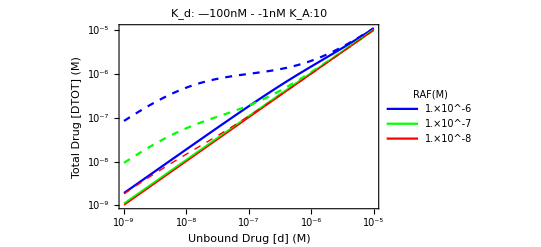

```mathematica
Sty[x_]:=Style[x,20,FontFamily->"Arial"];
KTarr={1. 10^-6,1. 10^-7,1. 10^-8};
kdarr={Kd-> 1. 10^-7 ,Kd-> 1. 10^-9};
pltfn=Flatten[Table[fnDTOT/.kd,{kd,kdarr},{RAF,KTarr}]]/.baseparams;
ps={Blue,Green,Directive[Red,Thick],Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Red,Dashed,Thick]};
LogLogPlot[pltfn,{d,10^-9,10^-5},Frame->True,FrameTicksStyle->20,PlotStyle->ps,PlotLegends->Placed[LineLegend[ {Blue,Green,Directive[Red,Thick]},Sty/@KTarr,LegendLabel->Sty["RAF(M)"],LegendFunction->Panel,LabelStyle->12],{Right,Bottom}],FrameLabel->(Sty/@{"Unbound Drug [d] (M)","Total Drug [DTOT] (M)"}),ImageSize->{500},FrameStyle->Thickness[0.004],PlotLabel->Sty["K_d: —100nM  - -1nM K_A:10"](*N[TableForm[parset01,TableDirections->Row]]*)]
```

#### 1.4.5. Analytic Expressions for maximum Fold Change (FC)

Fold change is defined as the ratio between maximum RAF activity (no/conc of active protomers) to that in absence of drug

```mathematica
rafFC=SimplifyPars[fnActiveRAF/baselineActiveRAF]
```

(f g^2 (f+d_rel) (1+KA+d_rel-√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g)))^2)/((f g+2 g d_rel+d_rel^2)^2 (1+KA-√((1+KA)^2+8 RAF_rel))^2)

Activating Range is defined as the lowest concentration above which the drug no longer acts as a paradoxical activator and becomes an inhibitor. This function is not easily solved analytically, and to understand its variation within the range of parameters defined in conditions for PA above, is calculated numerically.

#### 1.4.6. Convert to Python

The analytic results of this model are only valid in some limits so to fully characterize the model, we use a semi-analytic approach where we solve analytically simplified expressions numerically.

Python implementation of the full model works best if we analytically solve unbound 14-3-3 as a function of unbound RAF (A) and undbound drug (d) and then solve the RAF and Drug conservation equations numerically.

Run the block ‘Analytic solutions of the model’ before converting to python

```mathematica
eqnsconsrv
```

{A (d+Kd+KA Kd+(2 A (d^2+2 d g Kd+f g Kd^2))/(f g Kd Kdim))==Kd RAF,d+(A d)/Kd+(2 A^2 d (d+g Kd))/(f g Kd^2 Kdim)==DTOT}

```mathematica
baseparams=Join[baseparams,{Kd->0.1}]
```

{KA→10,Kdim→0.1,RAF→0.4,f→0.01,g→100,Kd→0.1}

```mathematica
fnActiveRAF
DTOTeqnLHS=SimplifyPars[eqnsconsrv[[2]][[1]]/.d->Subscript[d, rel] Kd]
```

(f g^2 (f+d_rel) (1+KA+d_rel-√((1+KA+d_rel)^2+(8 (f g+2 g d_rel+d_rel^2) RAF_rel)/(f g)))^2)/(8 (f g+2 g d_rel+d_rel^2)^2 RAF_rel)

(d_rel (g (2 A^2+A f Kdim+f Kd Kdim)+2 A^2 d_rel))/(f g Kdim)

```mathematica
(*String replacement functions to convert mathematica results into python*)
names1={KA,Kdim,Kd,RAF,f,g};
paramnames={KA,Kdim,Kd,RAF,f,g};
addparams[x_]:="params['"<>ToString[x]<>"']";
reppython=Join[{"^"->"**","Sqrt["->"np.sqrt(","]"->")","->"->":"},Thread[(ToString[#//InputForm]&/@paramnames)->(addparams/@names1)]];
(*Unbound RAF*)
tryAsol=Flatten[NSolve[{(RAFeqn==Kd RAF)/.baseparams/.{Subscript[d, rel]->Sqrt[2]/2},A≥0},A]]
(*Active Kinase*)
StringReplace[ToString[InputForm[fnActiveRAF/.{Subscript[RAF, rel]->RAF/Kdim,Subscript[d, rel]->d/Kd}]],reppython]
(*Validation*)
SetPrecision[fnActiveRAF/.{Subscript[RAF, rel]->RAF/Kdim}/.{Subscript[d, rel]->Sqrt[2]/2}/.baseparams,10]
```

{A→0.00995762}

(params['f']*params['g']**2*(params['f'] + d/params['Kd'])*params['Kdim']*(1 + params['KA'] + d/params['Kd'] - np.sqrt((1 + params['KA'] + d/params['Kd'])**2 + (8*(params['f']*params['g'] + d**2/params['Kd']**2 + (2*d*params['g'])/params['Kd'])*params['RAF'])/(params['f']*params['g']*params['Kdim'])))**2)/(8*(params['f']*params['g'] + d**2/params['Kd']**2 + (2*d*params['g'])/params['Kd'])**2*params['RAF'])

0.3555207692

```mathematica
(*RAF*)
StringReplace[ToString[InputForm[RAFeqn]],reppython]
(*Validation*)
SetPrecision[RAF-RAFeqn/.{A->0.001,Subscript[d, rel]->Sqrt[2]/2}/.baseparams,10]
```

(A*params['Kd']*(params['f']*params['g']*(2*A + params['Kdim'] + params['KA']*params['Kdim']) + params['g']*(4*A + params['f']*params['Kdim'])*dr + 2*A*dr**2))/(params['f']*params['g']*params['Kdim'])

0.3985434466

```mathematica
SetPrecision[DTOTeqnLHS/.tryAsol/.{Subscript[d, rel]->Sqrt[2]/2}/.baseparams,10]
```

0.2189685447

```mathematica
(*Drug*)
DTOTeqnLHSA=SimplifyPars[(DTOTeqnLHS/.sol4A)/.{Subscript[RAF, rel]->RAF/Kdim,Subscript[d, rel]->d/Kd}];
StringReplace[ToString[InputForm[DTOTeqnLHSA]],reppython]
(*Validation*)
SetPrecision[DTOTeqnLHSA/.{d->Kd*Sqrt[2]/2}/.baseparams,10]
```

(d*(8*(d**2 + 2*d*params['g']*params['Kd'] + params['f']*params['g']*params['Kd']**2)**2 - 2*params['f']*params['g']*(d**2 + 2*d*params['g']*params['Kd'] + params['f']*params['g']*params['Kd']**2)*params['Kdim']*(d + params['Kd'] + params['KA']*params['Kd'] - np.sqrt((d + params['Kd'] + params['KA']*params['Kd'])**2 + (8*(d**2 + 2*d*params['g']*params['Kd'] + params['f']*params['g']*params['Kd']**2)*params['RAF'])/(params['f']*params['g']*params['Kdim']))) + d*params['f']*params['g']*params['Kdim']*(d + params['Kd'] + params['KA']*params['Kd'] - np.sqrt((d + params['Kd'] + params['KA']*params['Kd'])**2 + (8*(d**2 + 2*d*params['g']*params['Kd'] + params['f']*params['g']*params['Kd']**2)*params['RAF'])/(params['f']*params['g']*params['Kdim'])))**2 + params['f']*params['g']**2*params['Kd']*params['Kdim']*(d + params['Kd'] + params['KA']*params['Kd'] - np.sqrt((d + params['Kd'] + params['KA']*params['Kd'])**2 + (8*(d**2 + 2*d*params['g']*params['Kd'] + params['f']*params['g']*params['Kd']**2)*params['RAF'])/(params['f']*params['g']*params['Kdim'])))**2))/(8*(d**2 + 2*d*params['g']*params['Kd'] + params['f']*params['g']*params['Kd']**2)**2)

0.2189685447

All the numerically output values are compared with respective python output to validate the function transfer.

### Section 1.5. Unified Model: fully-analytic solution to special case where g=f

```mathematica
Quit[]
```

#### 1.5.1. Analytic Solution to the model

This model is a solvable limit to the general all-mechanisms model and can therefore be used to test some of the analytic results. However, it is not compatible with the data. f<1 and g>1 respectively support PA mechanism and f>1 and g<1 do not. Therefore f=g with PA extant would mean that the two mechanisms act in opposite  manner relative to PA. This may still be instructive as a theoretical limit applicable in dimer kinase inhibition where positive cooperativity as well as dimer stabilization mechanisms exist.

```mathematica
vars={a,A,d,AA,Ad,AAd,AdAd};(*A list of all variables*)
rep5={AA->A^2/Kdim,AAd->(2 A^2 d)/(f Kdim Kd),AdAd->(A^2 d^2)/(f g Kdim Kd^2),Ad->(A d)/Kd,a->A KA}/.g->f; (*derived from equilibrium relationships*)
Consrv[eqns_]:={Simplify[eqns[[1]]+eqns[[2]]+eqns[[5]]+2(eqns[[4]]+eqns[[6]]+eqns[[7]])],Simplify[eqns[[3]]+eqns[[5]]+eqns[[6]]+2(eqns[[7]])]};(*conservation relations for RAF and DTOT*)
eqnsconsrv=Simplify[Thread[Simplify[Consrv[vars]/.rep5]=={RAF,DTOT}]]
```

{A f (d+Kd+KA Kd)+(2 A^2 (d+f Kd)^2)/(f Kd Kdim)==f Kd RAF,d+(A d)/Kd+(2 A^2 d (d+f Kd))/(f^2 Kd^2 Kdim)==DTOT}

A simultaneous solution to both the above conservation equations is unwieldy and hard to obtain. Instead, we find partial solutions for kinase protomers as a function of free drug and then free drug as a function of the total drug and the kinase protomers. The latter solution is used to numerically construct d vs DTOT relationship.

```mathematica
SimplifyPars[x_]:=Simplify[x,{RAF>0,DTOT>0,Kd>0,Kdim>0,KA>0,d>0,f>0,g>0,Subscript[d, rel]>0,Subscript[RAF, rel]>0}];
sol5A=SimplifyPars[Solve[eqnsconsrv[[1]],A]][[2]]  (*Second solution is positive*)
sol5d=SimplifyPars[Solve[eqnsconsrv[[2]],d]][[2]](*Second solution is positive*)
```

{A→-(f Kd Kdim (d f+f Kd+f KA Kd-√(f^2 (d+Kd+KA Kd)^2+(8 (d+f Kd)^2 RAF)/Kdim)))/(4 (d+f Kd)^2)}

{d→-(f Kd (2 A^2+A f Kdim+f Kd Kdim-√(8 A^2 DTOT Kdim+(2 A^2+A f Kdim+f Kd Kdim)^2)))/(4 A^2)}

We estimate the total activity by counting all of the drug-free protomers which occur within a partly active or fully active dimer. Substituting the above solution into the expression for Raf activity and dividing by total RAF concentration, we obtain the proportionate activity as a function of total drug and other parameters.

```mathematica
RafActivity[vars_]:= 2 vars[[4]] + vars[[6]]
fnActiveRAF5=SimplifyPars[RafActivity[vars]/RAF/.rep5/.sol5A];
repratios={Kdim->RAF/Subscript[RAF, rel],d->Kd Subscript[d, rel]};
fnActiveRAF5=SimplifyPars[FullSimplify[fnActiveRAF5/.repratios]]
fnActiveRAF52=FullSimplify[SimplifyPars[fnActiveRAF5//.{KA->E1c-1-Subscript[d, rel],Subscript[RAF, rel]->E2u2 *f/(f+Subscript[d, rel] (2+f Subscript[d, rel])) /8}]]
```

(f (f+f KA+f d_rel-√(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel))^2)/(8 (f+d_rel)^3 RAF_rel)

((f+d_rel (2+f d_rel)) (-E1c f+√(f (E1c^2 f+(E2u2 (f+d_rel)^2)/(f+d_rel (2+f d_rel)))))^2)/(E2u2 (f+d_rel)^3)

Note that the above equations represent the total active RAF protomers in proportion to the total RAF kinase as a function of unbound drug (d). In order to analytically establish parameter values which correspond to activation of the kinase, we find the first derivative of this function (equation 11) and search for it’s zeroes (equation 12).

```mathematica
RafDimers[eqns_]:=(eqns[[4]]+eqns[[6]]+eqns[[7]]);
fnDimers5=FullSimplify[SimplifyPars[(RafDimers[vars]/RAF/.rep5/.sol5A)/.repratios]]
SimplifyPars[fnDimers5/fnActiveRAF5]
```

((-f (1+KA+d_rel)+√(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel))^2)/(16 (f+d_rel)^2 RAF_rel)

(f+d_rel)/(2 f)

##### 4.2. Baseline Signaling (drug - free)

```mathematica
baselineActiveRAF5=fnActiveRAF5/.Subscript[d, rel]->0;
rep3b5={Subscript[RAF, rel]->E3(1+KA)^2/8};
baselineActiveRAF15=SimplifyPars[baselineActiveRAF5/.rep3b5]
SimplifyPars[D[baselineActiveRAF15,E3]/.rep3b5]
```

(-1+√(1+E3))^2/E3

(-1+√(1+E3))^2/(E3^2 √(1+E3))

The derivative of baseline signaling relative to E3 is a positive definite function. Therefore, baseline signaling is a monotonically proportionate to E3, which is in turn, monotonically proportionate to RAF concentration and monotonically inverse relationship to KA.

Hence in the base model, increasing KA decreases baseline signaling and increasing RAF_rel  increases baseline signaling.

#### 1.5.3. Conditions on parameter regions for activation in response to the drug

```mathematica
dfn5=SimplifyPars[D[fnActiveRAF5,Subscript[d, rel]]]
```

(f (f+f KA+f d_rel-√(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel)) (2 (f+d_rel) (f-(2 f^2 (1+KA+d_rel)+16 (f+d_rel) RAF_rel)/(2 √(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel)))-3 (f+f KA+f d_rel-√(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel))))/(8 (f+d_rel)^4 RAF_rel)

```mathematica
zeroes5=SimplifyPars[Solve[dfn5==0,Subscript[d, rel],VerifySolutions->True]]
```

{{d_rel→-(f (f+f KA+8 RAF_rel+2 Abs[1-f+KA] √(f^2+6 RAF_rel)))/(f^2+8 RAF_rel)},{d_rel→-(f (f+f KA+8 RAF_rel-2 Abs[1-f+KA] √(f^2+6 RAF_rel)))/(f^2+8 RAF_rel)}}

The first solution is negative definite. Below, we derive the rules (expression 13) which allow the second solution to be positive

```mathematica
exist5=SimplifyPars[Reduce[((Subscript[d, rel]/.zeroes5[[2]])>0)&&(KA>0)&&(Subscript[RAF, rel]>0)]]
```

4 f^2+3 (1+KA)^2>8 (f+f KA+RAF_rel)&&(2 f<1+KA||2 f>3+3 KA)

```mathematica
d2fn5=SimplifyPars[D[dfn5,Subscript[d, rel]]]
```

1/(8 (f+d_rel)^5 RAF_rel)f ((f+d_rel) (-f-(16 f^2 (1-f+KA)^2 (f+d_rel) RAF_rel)/((f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel)^(3/2))+(2 f^2 (1+KA+d_rel)+16 (f+d_rel) RAF_rel)/(2 √(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel))) (f+f KA+f d_rel-√(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel))+(f+d_rel) (f-(2 f^2 (1+KA+d_rel)+16 (f+d_rel) RAF_rel)/(2 √(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel))) (2 (f+d_rel) (f-(2 f^2 (1+KA+d_rel)+16 (f+d_rel) RAF_rel)/(2 √(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel)))-3 (f+f KA+f d_rel-√(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel)))-4 (f+f KA+f d_rel-√(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel)) (2 (f+d_rel) (f-(2 f^2 (1+KA+d_rel)+16 (f+d_rel) RAF_rel)/(2 √(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel)))-3 (f+f KA+f d_rel-√(f^2 (1+KA+d_rel)^2+8 (f+d_rel)^2 RAF_rel))))

```mathematica
d2fn5z=SimplifyPars[d2fn5/.zeroes5[[2]]]
```

Piecewise[{{-((f^2+8 RAF_rel)^2 (4 RAF_rel+f (f-√(f^2+6 RAF_rel))) (RAF_rel (6 f-4 √(f^2+6 RAF_rel))+f^2 (f-√(f^2+6 RAF_rel))))/(4 f^2 (-1+f-KA)^3 RAF_rel (f-2 √(f^2+6 RAF_rel))^4), f≤1+KA}, {((f^2+8 RAF_rel)^2 (12 RAF_rel+f (f-√(f^2+6 RAF_rel))) (1296 RAF_rel^2+6 f RAF_rel (45 f-16 √(f^2+6 RAF_rel))+13 f^3 (f-√(f^2+6 RAF_rel))))/(4 f^2 (-1+f-KA)^3 RAF_rel (f+2 √(f^2+6 RAF_rel))^5), True}}]

```mathematica
d2fn5z[[1]][[1,1]]
```

-((f^2+8 RAF_rel)^2 (4 RAF_rel+f (f-√(f^2+6 RAF_rel))) (RAF_rel (6 f-4 √(f^2+6 RAF_rel))+f^2 (f-√(f^2+6 RAF_rel))))/(4 f^2 (-1+f-KA)^3 RAF_rel (f-2 √(f^2+6 RAF_rel))^4)

```mathematica
exist5d2=SimplifyPars[SimplifyPars[Reduce[(d2fn5z[[1]][[1,1]]<0)&&(KA>=0)&&(Subscript[RAF, rel]>=0)]]]
```

f<1||1+KA>f

The f<1 condition comes naturally from the equations. The alternative is that KA>1+f so PA exists even when f>1.

```mathematica
SimplifyPars[SimplifyPars[Reduce[(d2fn5z[[2]]<0)&&(KA>=0)&&(Subscript[RAF, rel]>=0)]]]
```

f<1||1+KA>f

```mathematica
exist5A=FullSimplify[exist5&&exist5d2]
```

4 f^2+3 (1+KA)^2>8 (f+f KA+RAF_rel)&&(2 f<1+KA||2 f>3+3 KA)&&(f<1||1+KA>f)

These are the full set of conditions for PA to exist in the model. The conditions above require f<(1+KA)/2. This is because considering the last two ‘AND’ conditions, if f>3/2(1+KA) it cannot simultaneously satisfy either of the last two conditions. Therefore, f <(1+KA)/2 needs to be satisfied. Under this condition, if f<1, it is automatically satisfied that f<(1+KA)/2 as long as KA>1. If f<(1+KA)/2, the last condition is automatically satisfied that f<1+KA.

```mathematica
exist5A1=f<(1+KA)/2
```

f<(1+KA)/2

```mathematica
exist5full=SimplifyPars[Reduce[exist5A&&exist5A1]]
```

2 f<1+KA&&8 (f+f KA+RAF_rel)<4 f^2+3 (1+KA)^2

#### 1.5.4. Monotonic relationship between unbound (d) and total (DTOT) drug concentrations

The derivative of the function DTOT relative to d is the sum of the derivative of different terms within the second equation in expression (1). Among these the derivative of the first term is 1. And the derivative of the second and third term are shown as non-negative functions of unbound drug d, below.

```mathematica
eqnsconsrv[[2]]
```

d+(A d)/Kd+(2 A^2 d (d+f Kd))/(f^2 Kd^2 Kdim)==DTOT

```mathematica
sd511=FullSimplify[SimplifyPars[D[A*d/.sol5A,d]]];
rd511=Reduce[sd511<0];
rd511s=SimplifyPars[rd511]
```

f>1+KA&&(d (1-2 f+KA)==f (1+KA) Kd||(RAF>((1+KA) (d (1-2 f+KA)-f (1+KA) Kd) Kdim)/(8 (d+f Kd))&&f (2 d+Kd+KA Kd)<d (1+KA)))

Note that the first condition, f be larger than 1+KA and the conditions derived for PA, that f<(1+KA)/2 cannot be simultaneously satisfied. Therefore, drugs that display PA have positive or 0 value for the derivative sd511.

```mathematica
SimplifyPars[Reduce[rd511s&&exist5A1]]
```

False

Therefore, when PA exists, the function sd511 cannot be negative.

```mathematica
sd512=SimplifyPars[D[Simplify[A^2 d (d+f Kd)/.sol5A],d]]
```

1/(16 (d+f Kd)^4)f^2 Kd^2 Kdim^2 (d f+f Kd+f KA Kd-√(f^2 (d+Kd+KA Kd)^2+(8 (d+f Kd)^2 RAF)/Kdim)) (2 d (d+f Kd) (f-(2 f^2 (d+Kd+KA Kd)+(16 (d+f Kd) RAF)/Kdim)/(2 √(f^2 (d+Kd+KA Kd)^2+(8 (d+f Kd)^2 RAF)/Kdim)))-3 d (d f+f Kd+f KA Kd-√(f^2 (d+Kd+KA Kd)^2+(8 (d+f Kd)^2 RAF)/Kdim))+(d+f Kd) (d f+f Kd+f KA Kd-√(f^2 (d+Kd+KA Kd)^2+(8 (d+f Kd)^2 RAF)/Kdim)))

Note that the first non-trivial product term in this expression is negative definite as the term inside the square root is always greater than the term outside. So we focus on the second term.

```mathematica
sd5121=SimplifyPars[sd512[[-1]]];
rd512=Reduce[sd5121>0];
```

```mathematica
rd512s=SimplifyPars[SimplifyPars[rd512]]
```

RAF<((d^2 (3 f^2-8 f (1+KA)+4 (1+KA)^2)-2 d f^2 (1+KA) Kd-f^2 (1+KA)^2 Kd^2) Kdim)/(8 (d+f Kd)^2)&&(1+KA) (2 d+f Kd)<d f

Again, notice the second necessary condition.

```mathematica
SimplifyPars[Reduce[rd512s[[-1]]&&exist5A1]]
```

False

When PA exists, the function sd5121 is never positive. And since its coefficient is always negative, therefore sd512 is positive or 0.

Finally,

DTOT=d+sd511/Kd+sd512/(f^2 Kd^2 Kdim)

Since all three expressions on RHS are non-negative derivatives as a function of unbound drug - the total drug has a non-negative derivative. Therefore, DTOT(d) is monotonically positive/increasing function.

```mathematica
fnDTOT=SimplifyPars[Consrv[vars][[2]]/.rep5/.sol5A];
```

#### 1.5.5. Analytic Expressions for maximum Fold Change (FC)

Fold change is defined as the ratio between maximum RAF activity (no/conc of active protomers) to that in absence of drug

```mathematica
maxActiveRAF5=FullSimplify[SimplifyPars[fnActiveRAF5/.zeroes5[[2]]]];
rafFC5=SimplifyPars[maxActiveRAF5/baselineActiveRAF5]
```

(4 (f^2+8 RAF_rel) (4 (-1+f-KA) RAF_rel+Abs[1-f+KA] (8 RAF_rel+f (f-√(f^2+6 RAF_rel))))^2)/((f (-1+f-KA)+2 Abs[1-f+KA] √(f^2+6 RAF_rel))^3 (1+KA-√((1+KA)^2+8 RAF_rel))^2)

When the ‘exist’ conditions derived above to qualify for existence of PA within this model are satisfied, we can evaluate the functional dependence of the raf fold change expression on RAF_rel and KA:

```mathematica
dRAFrafFC5=SimplifyPars[D[rafFC5,Subscript[RAF, rel]]];
dKArafFC5=SimplifyPars[D[rafFC5,KA]];
dfrafFC5=SimplifyPars[D[rafFC5,f]];
```

```mathematica
Simplify[SimplifyPars[Reduce[dRAFrafFC5<0]],exist5A1]
```

4 f^2+3 (1+KA)^2>8 (f+f KA+RAF_rel)

Under typical conditions for PA, f<1 and KA>1. Therefore the above condition is pretty easy to satisfy with RAF<<Kdim. That is when RAF has a low concentration or weakly dimerizes. In that case, RAF increase reduces fold change.
However, with stronger dimerization or very high, likely super-physical RAF concentration(~100 micro-molar), it may be possible to invert the curve, however, the same condition is derived for PA, therefore, the increasing RAF concentration will keep reducing fold change until no PA is observed. Monotonically.

```mathematica
exist5full
```

2 f<1+KA&&8 (f+f KA+RAF_rel)<4 f^2+3 (1+KA)^2

Activating Range is defined as the lowest concentration above which the drug no longer acts as a paradoxical activator and becomes an inhibitor. This function is not easily solved analytically, and to understand its variation within the range of parameters defined in conditions for PA above, is calculated numerically.

## Descriptive, example Plots (supp text section 3)

Plots for individual curves. Run all 1st sub sections (*.1) for any ONE of sections 1-4 to get the following plots.

```mathematica
Sty[x_]:=Style[x,22,Bold,FontFamily->"Times"];
```

```mathematica
plfn1=({fnActiveRAFDS/(fnActiveRAFDS/.Subscript[d, rel]->0),fnActiveRAFNC/(fnActiveRAFNC/.Subscript[d, rel]->0),fnActiveRAFCA/(fnActiveRAFCA/.Subscript[d, rel]->0),fnActiveRAF/(fnActiveRAF/.Subscript[d, rel]->0)}/.{Subscript[RAF, rel]->RAF/Kdim}/.baseparams);
```

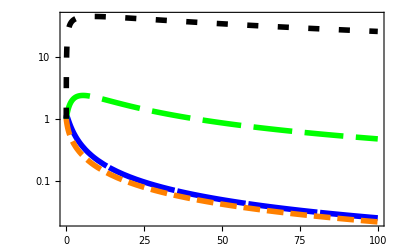

```mathematica
legendlist = Sty["AK\n"];
rvals={2.,0.03,0.07,0.02};
r1={Tiny,Small,Medium,Large};
cols={Blue,Orange,Green,Black};
cs = Table[Directive[ Thickness[0.01], cols[[i]],Dashing[{rvals[[i]],r1[[i]]}]],{i,4}]; (*dashing style by model*)
LogPlot[plfn1, {Subscript[d, rel], 0, 100}, Frame -> True,(*FrameLabel->(Sty/@{"Relative Unbound Drug Concentration","RAF Complex Molecules"}),*)ImageSize -> {500}, FrameStyle -> Thickness[0.004], FrameTicksStyle -> Directive[25, Black], PlotRange -> Full, PlotStyle ->cs, PlotLegends -> "AK"]
```

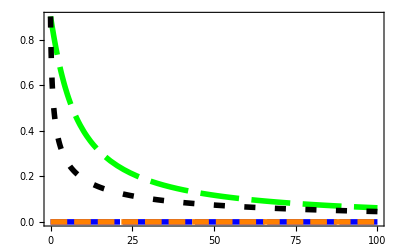
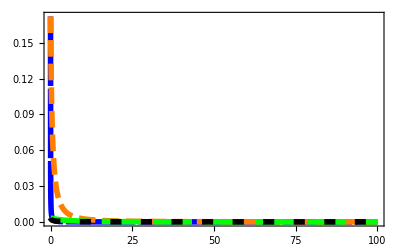
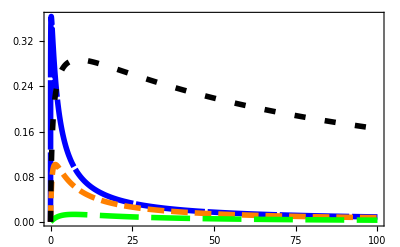
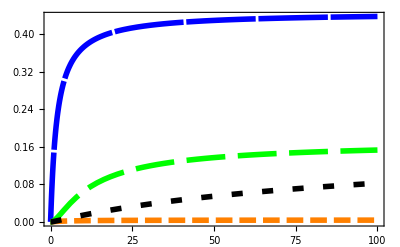
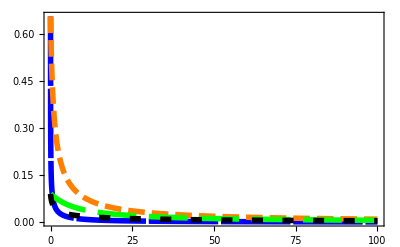
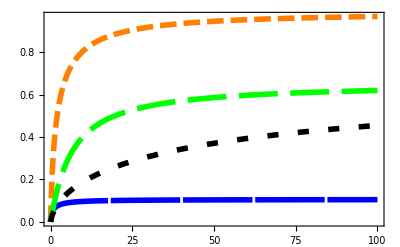

```mathematica
fn2part[1]=SimplifyPars[(({a,AA,AAd,AdAd,A,Ad}/.rep1/.sol1A)/RAF/.d->(Subscript[d, rel] Kd))/.baseparams];
fn2part[2]=SimplifyPars[(({a,AA,AAd,AdAd,A,Ad}/.rep2/.sol2A)/RAF/.d->(Subscript[d, rel] Kd))/.baseparams];
fn2part[3]=SimplifyPars[(({a,AA,AAd,AdAd,A,Ad}/.rep3/.sol3A)/RAF/.d->(Subscript[d, rel] Kd))/.baseparams];
fn2part[4]=SimplifyPars[(({a,AA,AAd,AdAd,A,Ad}/.rep4/.sol4A)/RAF/.d->(Subscript[d, rel] Kd))/.baseparams];
plfn =SimplifyPars[Table[fn2part[i][[j]],{j,6},{i,4}]];
legendlist = Sty /@ { "a\n", "AA\n", " AAd\n", " AdAd\n", " A\n", " Ad\n"};
Table[Plot[Evaluate[plfn[[i]]], {Subscript[d, rel], 0, 100}, Frame -> True,ImageSize -> {500}, FrameStyle -> Thickness[0.004], FrameTicksStyle -> Directive[25, Black], PlotRange -> All, PlotStyle ->cs, PlotLegends -> legendlist[[i]]],{i,Length[plfn]}]
```